### Start choosing the example:

```mathematica
t="Paper example";
(*Get["/Users/salehfh/downloads/MFGraphs-master/MFGraphs/Examples/ExamplesParameters.m"]*)
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"]
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"]
beta=1;
g[x]
```

x

```mathematica
Data=DataG[t]
```

```mathematica
Data=<|"Vertices List"->{2,3},"Adjacency Matrix"->{{0,1},{0,0}},"Entrance Vertices and Currents"->{{2,I1},{3,I2}},"Exit Vertices and Terminal Costs"->{{2,0},{3,0}},"Switching Costs"->{{1,2,3,S1},{3,2,1,S2}}|>
```

<|Vertices List→{2,3},Adjacency Matrix→{{0,1},{0,0}},Entrance Vertices and Currents→{{2,I1},{3,I2}},Exit Vertices and Terminal Costs→{{2,0},{3,0}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
CoefficientArrays
```

```mathematica
d2e=D2E[Data/.{I1->3,I2->6,S1->0,S2->0}];
d2e["jvars"]
d2e["jtvars"]
d2e["InitRules"]
d2e["RulesCriticalCase"]
```

D2E: Variables are all set

Second check:

The matrices B and K are: 
{(3
6
0
0
0
0
0
0),(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | 0 | 0
-1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}
The order of the variables is 
{j1,j10,j2,j4,j6,j8,jt1,jt10,jt11,jt12,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9}

{u4→0,u6→0}

D2E: CleanEqualities for the values at the auxiliary edges

D2E: Assembled most elements of the system

D2E: CleanEqualities for the switching conditions on each vertex: 
(u5∈ℝ&&u3==u8&&u1==u8&&u2≤u5&&u10≤u2)||((u5|u8)∈ℝ&&u2≤u5&&u10≤u2&&u3>u8&&u8≤u1≤u3)

D2E: CleanEqualities for the complementary conditions (given the rules)

D2E: CleanEqualities for the balance conditions in terms of (mostly) transition currents

D2E: CleanEqualities for the (non) critical case equations

D2E: D2E is finished!

<|{2,2->3}→j1,{3,2->3}→j2,{2,2->ex2}→j3,{ex2,2->ex2}→j4,{3,3->ex3}→j5,{ex3,3->ex3}→j6,{en2,en2->2}→j7,{2,en2->2}→j8,{en3,en3->3}→j9,{3,en3->3}→j10|>

<|{2,2->3,2->ex2}→jt1,{2,2->3,en2->2}→jt2,{2,2->ex2,2->3}→jt3,{2,2->ex2,en2->2}→jt4,{2,en2->2,2->3}→jt5,{2,en2->2,2->ex2}→jt6,{3,2->3,3->ex3}→jt7,{3,2->3,en3->3}→jt8,{3,3->ex3,2->3}→jt9,{3,3->ex3,en3->3}→jt10,{3,en3->3,2->3}→jt11,{3,en3->3,3->ex3}→jt12|>

<|j2→jt5,j4→3+jt11-jt5,j7→0,j1→jt11,j6→6-jt11+jt5,j9→0,j8→3,j10→6,j3→0,j5→0,u4→0,u6→0,u3→0,u5→0,u8→u7,u9→u10,jt10→0,jt2→0,jt3→0,jt4→0,jt8→0,jt9→0,jt1→jt11,jt12→6-jt11,jt6→3-jt5,jt7→jt5|>

<|j2→jt5,j4→3+jt11-jt5,j7→0,j1→jt11,j6→6-jt11+jt5,j9→0,j8→3,j10→6,j3→0,j5→0,u4→0,u6→0,u3→0,u5→0,u8→u7,u9→u10,jt10→0,jt2→0,jt3→0,jt4→0,jt8→0,jt9→0,jt1→jt11,jt12→6-jt11,jt6→3-jt5,jt7→jt5,u2→jt11-jt5+u1|>

```mathematica
us=d2e["uvars"]/@Join[OtherWay/@(Select[d2e["jvars"],Function[xx,xx==#]]&/@(Variables/@(d2e["EqEntryIn"]/.Equal->Plus)//Flatten)//Keys//Flatten[#,1]&),d2e["NoDeadEnds"]]
```

{u7,u9,u1,u3,u8,u2,u5,u10}

```mathematica
d2e["K"]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | 0 | 0
-1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
us.d2e["K"]
%.d2e["vars"]
```

{u1-u2,u10+u9,-u1+u2,-u3,-u5,u7+u8,-u1+u3,u10-u5,-u10+u2,-u10+u5,-u1+u8,u1-u3,-u3+u8,u1-u8,u3-u8,-u2+u5,u10-u2,u2-u5}

j1 (u1-u2)+jt8 (u10-u2)+j2 (-u1+u2)+jt11 (-u10+u2)+jt3 (u1-u3)-j4 u3+jt1 (-u1+u3)+jt10 (u10-u5)+jt9 (u2-u5)-j6 u5+jt12 (-u10+u5)+jt7 (-u2+u5)+jt5 (u1-u8)+jt6 (u3-u8)+jt2 (-u1+u8)+jt4 (-u3+u8)+j8 (u7+u8)+j10 (u10+u9)

```mathematica
d2e["uvars"]
d2e["jvars"]
d2e["jtvars"]
```

<|{2,2->3}→u1,{3,2->3}→u2,{2,2->ex2}→u3,{ex2,2->ex2}→u4,{3,3->ex3}→u5,{ex3,3->ex3}→u6,{en2,en2->2}→u7,{2,en2->2}→u8,{en3,en3->3}→u9,{3,en3->3}→u10|>

<|{2,2->3}→j1,{3,2->3}→j2,{2,2->ex2}→j3,{ex2,2->ex2}→j4,{3,3->ex3}→j5,{ex3,3->ex3}→j6,{en2,en2->2}→j7,{2,en2->2}→j8,{en3,en3->3}→j9,{3,en3->3}→j10|>

<|{2,2->3,2->ex2}→jt1,{2,2->3,en2->2}→jt2,{2,2->ex2,2->3}→jt3,{2,2->ex2,en2->2}→jt4,{2,en2->2,2->3}→jt5,{2,en2->2,2->ex2}→jt6,{3,2->3,3->ex3}→jt7,{3,2->3,en3->3}→jt8,{3,3->ex3,2->3}→jt9,{3,3->ex3,en3->3}→jt10,{3,en3->3,2->3}→jt11,{3,en3->3,3->ex3}→jt12|>

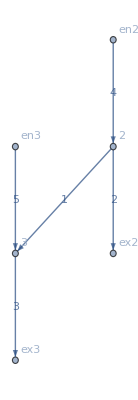

```mathematica
Graph[d2e["FG"],EdgeLabels->"Index"]
```

```mathematica
Keys[d2e]//Sort
```

{Adjacency Matrix,AllIneq,AllOr,B,BG,BoundaryRules,costpluscurrents,Entrance Vertices and Currents,EqAllAll,EqBalanceGatheringCurrents,EqBalanceSplittingCurrents,EqCriticalCase,EqCurrentCompCon,EqNonCritical,EqPosCon,EqPosJs,EqPosJts,EqSwitchingConditions,EqTransitionCompCon,EqValueAuxiliaryEdges,Exit Vertices and Terminal Costs,FG,InEdges,InitRules,jays,jtvars,jvars,K,MinimalTimeRhs,Nlhs,Nrhs,OutEdges,RuleEntryIn,RuleNonCritical,RuleNonCritical1,RulesCriticalCase,RulesCriticalCase1,Switching Costs,uvars,Vertices List}

```mathematica
d2e["EqNonCritical"]/.cpc1->0
```

-j1+j2-u1+u2==0

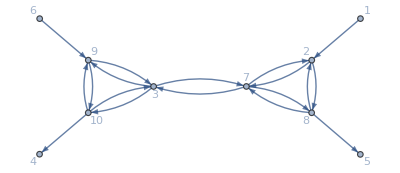

{{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,-1,-1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,-1,-1,-1,0,0,1,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,-1,-1,-1,0,0,1,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,1,-1,-1,-1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0,0,0,-1,-1,0,0,1},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,-1,-1,-1}}

```mathematica
grapho=AdjacencyGraph[{1,2,3,4,5,6,7,8,9,10},
{
{0,1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,1,1,0,0},
{0,0,0,0,0,0,1,0,1,1},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,1,0,0,1,0,1,0,0,0},
{0,0,1,0,0,0,0,0,0,1},
{0,0,1,1,0,0,0,0,1,0}
},VertexLabels->"Name",GraphLayout->"SpringElectricalEmbedding"]

incidencematrixgrapho =grapho//IncidenceMatrix//Normal
%//MatrixForm
%//IncidenceGraph
%//AdjacencyMatrix//MatrixForm
```